```mathematica
internoTriangolo={{Yellow,Polygon[{{0,0},{4,0},{0,3},{0,0}}]}};
bordoTriangolo={Thickness[.008],Line[{{0,0},{4,0},{0,3},{0,0}}]};
```

```mathematica
cateti={{Red,Polygon[{{0,0},{-3,0},{-3,3},{0,3}}]},{Green,Polygon[{{0,0},{0,-4},{4,-4},{4,0}}]},Line[{{0,0},{-3,0},{-3,3},{0,3}}],Line[{{0,0},{0,-4},{4,-4},{4,0}}]};
```

```mathematica
ipotenusa=Module[{t=ArcTan[3/4],trasformazioneAffine},
trasformazioneAffine[punto_List]:={0,3}+RotationMatrix[-t].punto;{{Red,Polygon[Map[trasformazioneAffine,{{0,0},{3Cos[ArcTan[4/3]],0},{3Cos[ArcTan[4/3]],5},{0,5},{0,0}}]]},{Green,Polygon[Map[trasformazioneAffine,{{3Cos[ArcTan[4/3]],0},{3Cos[ArcTan[4/3]],5},{5,5},{5,0},{3Cos[ArcTan[4/3]],0}}]]},Line[Map[trasformazioneAffine,{{3Cos[ArcTan[4/3]],-12/5},{3Cos[ArcTan[4/3]],5},{0,5},{0,0}}]],Line[Map[trasformazioneAffine,{{3Cos[ArcTan[4/3]],0},{3Cos[ArcTan[4/3]],5},{5,5},{5,0},{3Cos[ArcTan[4/3]],0}}]]}];
```

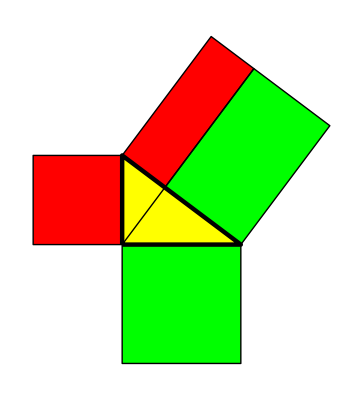

```mathematica
pitagora3=Graphics[{internoTriangolo,cateti,ipotenusa,bordoTriangolo},AspectRatio->Automatic]
```

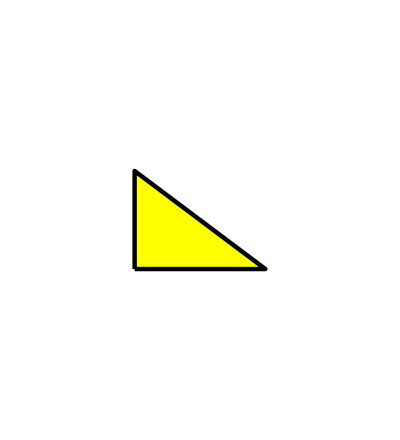

```mathematica
pitagora1=Show[Graphics[{internoTriangolo,bordoTriangolo}],Sequence@@AbsoluteOptions[pitagora3]]
```

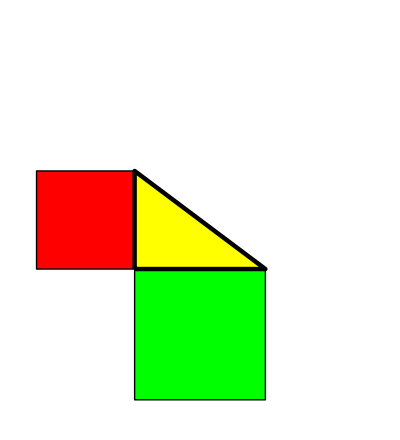

```mathematica
pitagora2=Show[Graphics[{internoTriangolo,cateti,bordoTriangolo}],Sequence@@AbsoluteOptions[pitagora3]]
```